# Slew Effect in SHARAQ04 PP Elastics

```mathematica
c = 299.792458;
mp=938.27203;
Bρ2T[m_,Z_,A_,Bρ_]:=1/A( √((Bρ Z c)^2+m^2)-m);
Tinc = Bρ2T[mp,1, 1, 2.47288];
z0Tpla = 1400;
T1[T_,α_]:=T Cos[α/2]^2
θ1[m_,T_,α_]:=ArcTan[√(T (2 m+T)) Cos[α/2]^2,(√(m T) Sin[α])/(√2)]
xpos[θ_]:=z0Tpla  Tan[θ-60°]
KE[θ_,T_]:=T/((2mp+T)/(2mp)Tan[θ]^2+1)
ToF[T_,θ_,m_,z0Tpla_,θd_]:=z0Tpla/(Cos[θd-θ]c √(1-(m/(m+T))^2))
xF=-1300;
xB=200;
Q[T_]:=25000000/(T+100)^2+1000
```

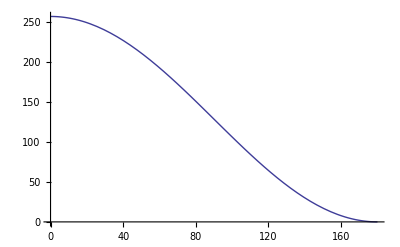

```mathematica
Plot[T1[Tinc,a Degree],{a, 0, 180}]
```

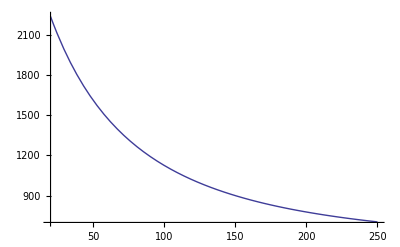

```mathematica
Plot[25000000/(T+100)^2+500,{T,20,250}]
```

## Monte Carlo

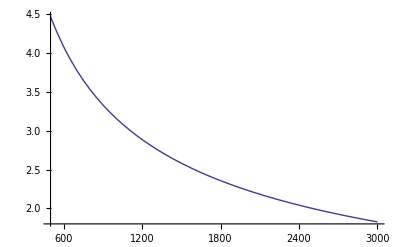

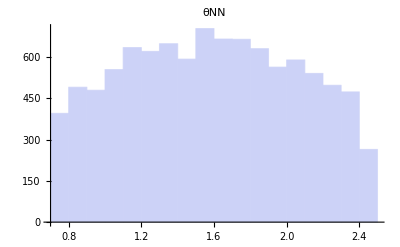

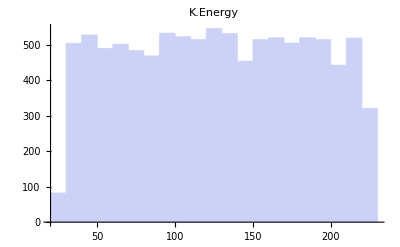

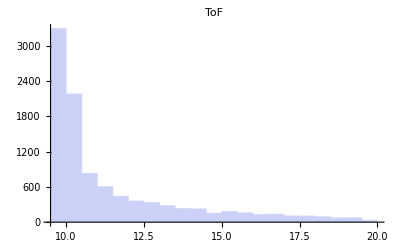

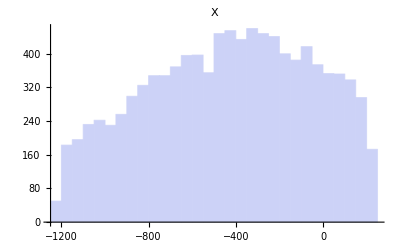

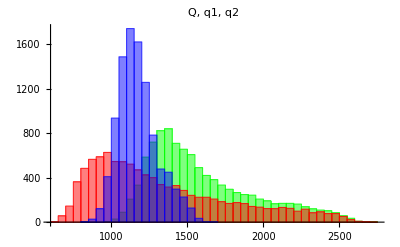

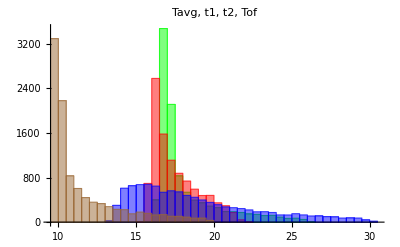

```mathematica
n=10000;
β=0.66;
a=3000;
Slew=100;
SlewP = 0.5;
walk[Q_]:=Slew/Power[Q,0.5];
Plot[walk[q],{q,500,3000}]
θNNList =Table[ArcCos[2RandomReal[{0.11,0.88}]-1],{i,1,n}];
EList=Table[T1[Tinc,θNNList[[i]]],{i,1,n}];
TofList = Table[ToF[EList[[i]],θ1[mp, Tinc,θNNList[[i]]], mp, z0Tpla, 60 °],{i,1,n}];
XList =Table[xpos[θ1[mp, Tinc,θNNList[[i]]]],{i,1,n}];
(*QList=Table[RandomReal[{500,2000}],{i,1,n}];*)
(*QList=RandomVariate[RayleighDistribution[5],n]*100+800;*)
(*QList=RandomVariate[PoissonDistribution[100],n]+0.1;*)
QList=Table[Q[EList[[i]]]+RandomVariate[NormalDistribution[0,100]],{i,1,n}];
q1List=Table[QList[[i]]Exp[-(Abs[XList[[i]]-xB]/a)],{i,1,n}];
w1List=Table[walk[q1List[[i]]],{i,1,n}];
t1List = Table[TofList[[i]]+Abs[XList[[i]]-xB]/(β c)+walk[q1List[[i]]]+RandomVariate[NormalDistribution[0,0.2]],{i,1,n}];
qt1List=Table[{t1List[[i]],q1List[[i]]},{i,1,n}];
q2List=Table[QList[[i]]Exp[-(Abs[XList[[i]]-xF]/a)],{i,1,n}];
w2List=Table[walk[q2List[[i]]],{i,1,n}];
t2List = Table[TofList[[i]]+Abs[XList[[i]]-xF]/(β c)+walk[q2List[[i]]]+RandomVariate[NormalDistribution[0,0.2]],{i,1,n}];
qt2List=Table[{t2List[[i]],q2List[[i]]},{i,1,n}];
TavgList=Table[(t1List[[i]]+t2List[[i]])/2,{i,1,n}];
q1TavgList=Table[{TavgList[[i]],q1List[[i]]},{i,1,n}];
Histogram[θNNList, PlotLabel->"θNN"]
Histogram[EList, PlotLabel->"K.Energy"]
Histogram[TofList, PlotLabel->"ToF"]
Histogram[XList, PlotLabel->"X"]
Histogram[{QList,q1List,q2List}, PlotLabel->"Q, q1, q2", ChartStyle->{Green, Red, Blue}]
Histogram[{TavgList,t1List,t2List,TofList}, PlotLabel->"Tavg, t1, t2, Tof", ChartStyle->{Green, Red, Blue, Brown}]
```

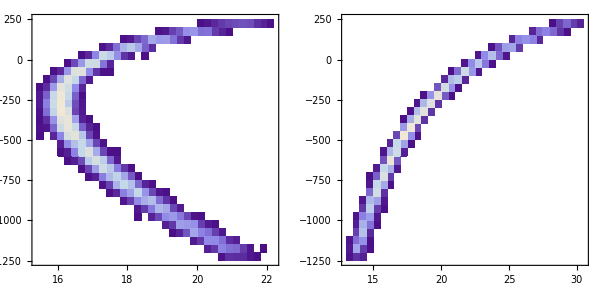

```mathematica
GraphicsGrid[{{
DensityHistogram[Table[{t1List[[i]],XList[[i]]},{i,1,n}]],
DensityHistogram[Table[{t2List[[i]],XList[[i]]},{i,1,n}]]
}},ImageSize->600]
```

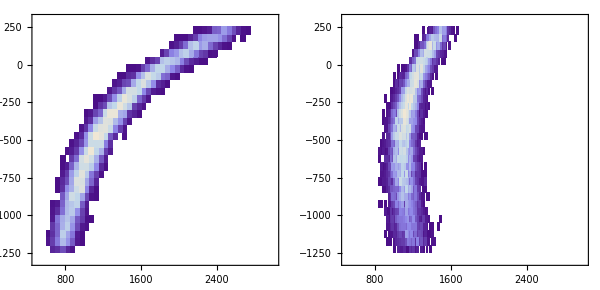

```mathematica
GraphicsGrid[{{
DensityHistogram[Table[{q1List[[i]],XList[[i]]},{i,1,n}],PlotRange->{{500,3000},{-1300,300}}],
DensityHistogram[Table[{q2List[[i]],XList[[i]]},{i,1,n}],PlotRange->{{500,3000},{-1300,300}}]
}},ImageSize->600]
```

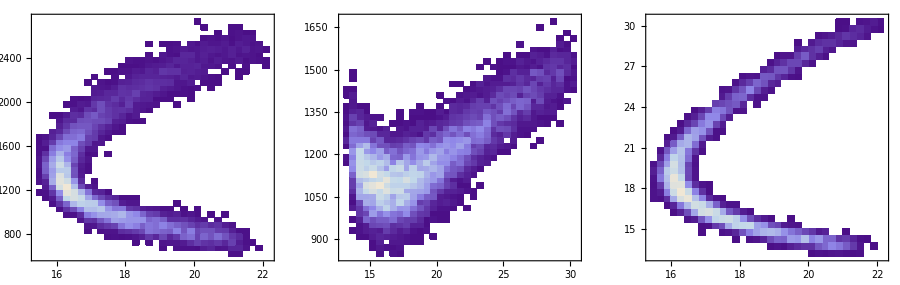

```mathematica
GraphicsGrid[{{
DensityHistogram[Table[{t1List[[i]],q1List[[i]]},{i,1,n}]],
DensityHistogram[Table[{t2List[[i]],q2List[[i]]},{i,1,n}]],
DensityHistogram[Table[{t1List[[i]],t2List[[i]]},{i,1,n}]]
}},ImageSize->900]
```

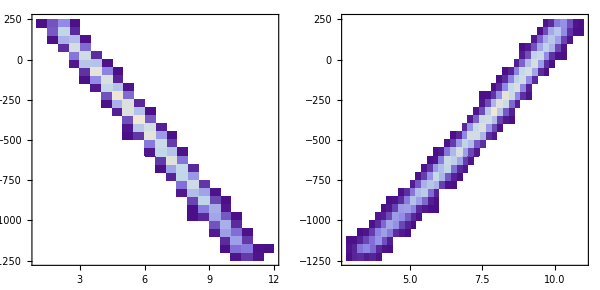

```mathematica
GraphicsGrid[{{
DensityHistogram[Table[{t1List[[i]]-TofList[[i]],XList[[i]]},{i,1,n}]],
DensityHistogram[Table[{t2List[[i]]-TofList[[i]],XList[[i]]},{i,1,n}]]
}},ImageSize->600]
```

```mathematica
s
```

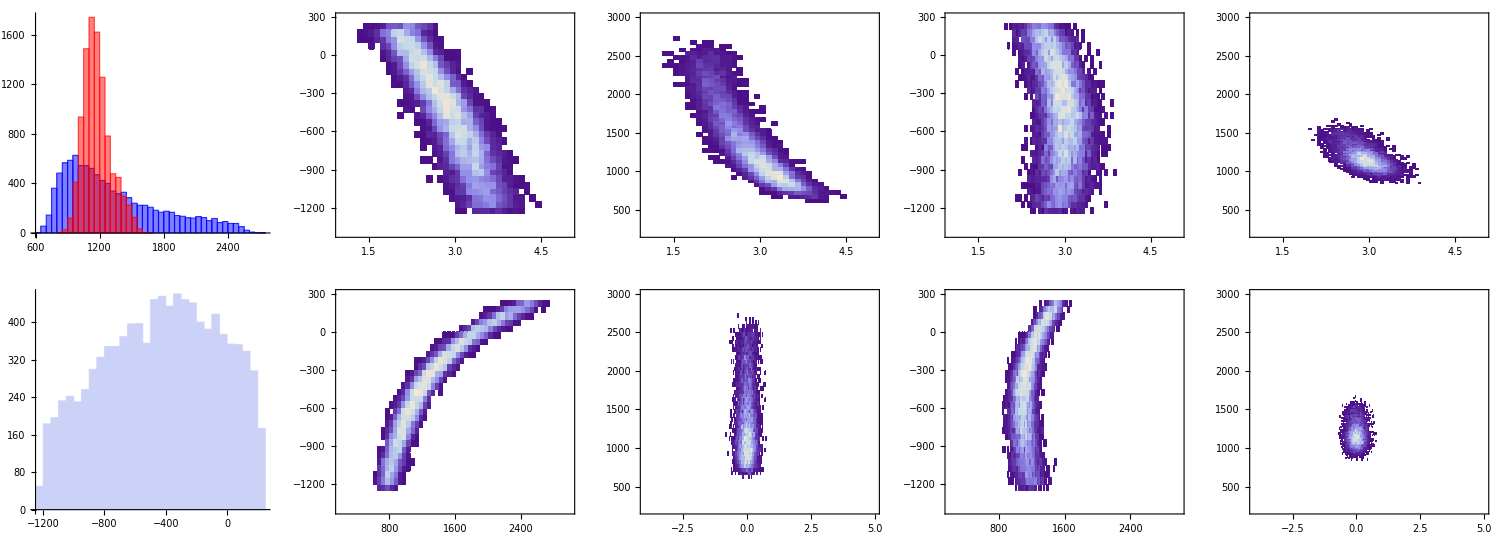

```mathematica
GraphicsGrid[{
{
Histogram[{q1List, q2List},ChartStyle->{Blue, Red}],
DensityHistogram[Table[{t1List[[i]]-TofList[[i]]-(xB-XList[[i]])/(β c),XList[[i]]},{i,1,n}],PlotRange->{{1,5},{-1400,300}}],
DensityHistogram[Table[{t1List[[i]]-TofList[[i]]-(xB-XList[[i]])/(β c),q1List[[i]]},{i,1,n}],PlotRange->{{1,5},{200,3000}}],
DensityHistogram[Table[{t2List[[i]]-TofList[[i]]-(XList[[i]]-xF)/(β c),XList[[i]]},{i,1,n}],PlotRange->{{1,5},{-1400,300}}],
DensityHistogram[Table[{t2List[[i]]-TofList[[i]]-(XList[[i]]-xF)/(β c),q2List[[i]]},{i,1,n}],PlotRange->{{1,5},{200,3000}}]
},
{Histogram[XList],

DensityHistogram[Table[{q1List[[i]],XList[[i]]},{i,1,n}],PlotRange->{{200,3000},{-1400,300}}],
DensityHistogram[Table[{t1List[[i]]-TofList[[i]]-(xB-XList[[i]])/(β c)-walk[q1List[[i]]],q1List[[i]]},{i,1,n}],PlotRange->{{-4,5},{200,3000}}],
DensityHistogram[Table[{q2List[[i]],XList[[i]]},{i,1,n}],PlotRange->{{200,3000},{-1400,300}}],
DensityHistogram[Table[{t2List[[i]]-TofList[[i]]-(XList[[i]]-xF)/(β c)-walk[q2List[[i]]],q2List[[i]]},{i,1,n}],PlotRange->{{-4,5},{200,3000}}]
}},ImageSize->1500]
```